## Ordinary Differential Equations

NDSolve[equns, vars, {t, t_min, t_max}]

```mathematica
sol = x[t]/.NDSolve[{x''[t] + 0.15x'[t]-x[t]+x[t]^3== 0.3Cos[t], x[0] == -1, x'[0]==1}, x, {t, 0, 50}]
```

{InterpolatingFunction[…][t]}

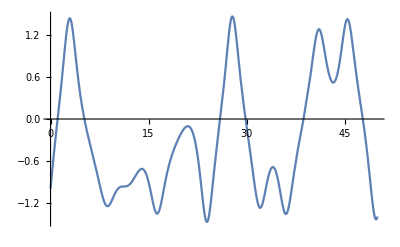

```mathematica
Plot[sol, {t, 0, 50}]
```

## Example: Lorenz Equations

```mathematica
sol = {x[t], y[t], x[t]} /. NDSolve[{x'[t] == -3 (x[t]-y[t]), y'[t] == -x[t]z[t]+ 26.5x[t]-y[t],
z'[t]==x[t]y[t]-z[t], x[0]==z[0]==0,y[0]==1},{x,y,z},{t, 0, 100},MaxSteps -> ∞]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

```mathematica
ParametricPlot3D[sol, {t,0,100}, PlotPoints-> 100]
```

-Graphics3D-

#### Demonstration of chaos and sensitivity to initial conditions

Solve the same system with slightly different initial conditions:

```mathematica
sol = First@NDSolve[{x'[t]==-3 (x[t] - y[t]),y'[t]==-x[t]z[t]+ 26.5x[t]-y[t],z'[t]==x[t]y[t]-z[t], x[0]==z[0]==0,y[0]==#},{x,y,z},{t,0,30}, MaxSteps->∞]&/@{1,0.9, 1.1}
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]},{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]},{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

```mathematica
sp[tn_] = {Specularity[White, 30], Orange, Sphere[{x[tn], y[tn],z[tn]}/.sol,1]};Animate[Graphics3D[sp[t],PlotRange->{{-15,15}, {-20, 20}, {0,40}},Background->Black], {t,0,30}, DefaultDuration->15] (* Three balls for three equations *)
```

## Partial Differential Equations

NDSolve[{eqns, ics, bcs}, vars, {t, t_min, t_max}, {x, x_min, x_max}, ...],
											vars = {u_1, u_2, ...},
								ics = {u_1[t, x,...] == a, u_2[0, x, ...]=b, ...},
								bcs = {u_1[t, x_min, ...] == c, u_1[t, x_max, ...]== d,
								       u_2[t, x_min, ...] == e, u_2[t, x_max,...]== f}

```mathematica
sol = u[t, x] /. NDSolve[{D[u[t,x],t]==D[u[t,x],x,x],u[0,x]==0, u[t,0]==Sin[t], u[t,5]==0}, u,{t,0,10}, {x,0,5}]
```

{InterpolatingFunction[…][t,x]}

```mathematica
Plot3D[sol, {t,0,10},{x,0,5}, PlotRange->All]
```

-Graphics3D-

## Hybrid Systems

NDSolve[{equn, ics, WhenEvent[pred, action]}, vars, {t, 0, tend}]

```mathematica
sol = y[t]/.NDSolve[{y''[t]==-9.81, y[0]==10, y'[0]==0, WhenEvent[y[t]==0, y'[t]->-0.7y'[t]]},y,{t,0,7}]
```

{InterpolatingFunction[…][t]}

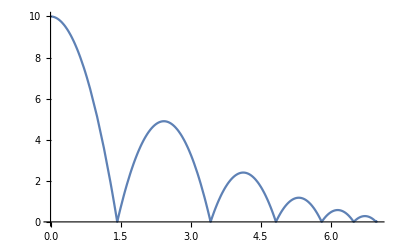

```mathematica
Plot[sol, {t,0,7}]
```

### Example: Poincare Section of Duffing Equation

```mathematica
data = Reap[NDSolve[{x''[t]+.15x'[t]-x[t]+x[t]^3==.3Cos[t],
x[0]==0, x'[0]==0, WhenEvent[Mod[t, 2π ]==0, Sow[{x[t], x'[t]}]]},{},{t,0,100000}, MaxSteps->∞]][[2]];
```

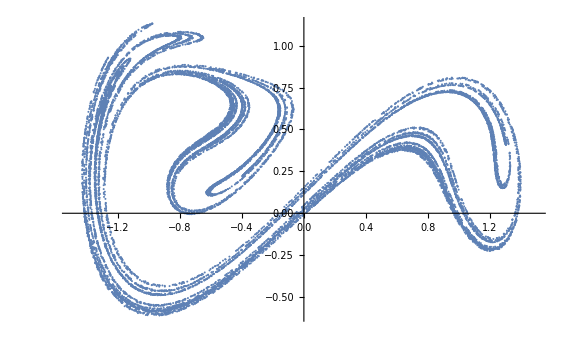

```mathematica
ListPlot[data, ImageSize->Large,PlotRange->{{-1.5,1.5},All}, PlotStyle->PointSize[0.0025]]
```

## Parametric Differential Equations

ParametricNDSolve[eqns, {u_1, u_2, ...}, {t, t_min, t_max}, pars]

```mathematica
sol = ParametricNDSolve[{x''[t]-x'[t]+x[t]==0, x[0]==1, x'[0]==s},x,{t,0,10},{s}]
```

{x→ParametricFunction[<>]}

```mathematica
x[1.5]/.sol
```

InterpolatingFunction[…]

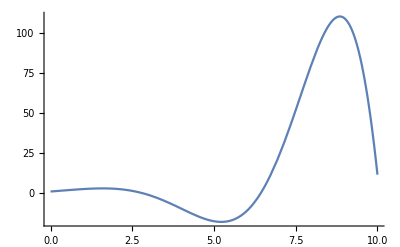

```mathematica
Plot[Evaluate[x[1.5][t] /. sol], {t,0,10}, PlotRange->All]
```

Find a parameter such that x[10] ==0.

```mathematica
FindRoot[Evaluate[x[s][10] /. sol], {s, 1}]
```

{s→1.40296}

### Example: Parameter Fitting to Data

```mathematica
data = {{0.5, 29.5}, {1.0,39.3},{1.5, 57.6},{2.,52.9},{2.5, 61.8},{3.,72.7},{3.5,89.3}, {4.,89.1},{4.5,79.0},{5.,92.0},{5.5,65.5},
{6., 66.1},{6.5,53.8}, {7.0, 46.1},{7.5,26.8},{8, 4.7},{8.5, -10.18},
{9.0, -40.9},{9.5,-65.4},{10.0, -79.7}};
```

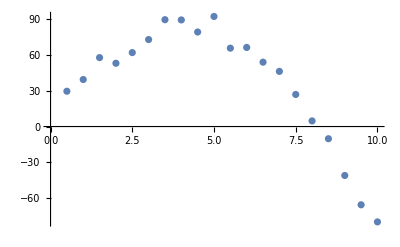

```mathematica
ListPlot[data]
```

Fit a differential equation of the form y’’(t ) = -wy(t), y(0) = a, y’(0) = b:

```mathematica
pfun = y/.ParametricNDSolve[{y''[t]==-w*y[t],  y[0]==a, y'[0]==b}, y,{t, 0, 10}, {w, a, b}]
```

```mathematica
ParametricFunction[<>]
```

ParametricFunction::noinfo: Input expression ParametricFunction[<>] contains insufficient information to interpret the result.

```mathematica
fit = FindFit[data, pfun[w, a, b][t],{{w, .1},{a, -1},{b, 1}},t]
```

{w→0.154688,a→-0.282608,b→35.5292}

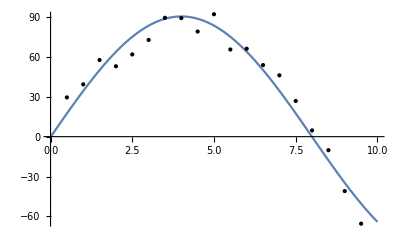

```mathematica
Plot[pfun[w,a, b][t]/.fit,{t,0,10}, Epilog->{Point@data}]
```

## Differential Algebraic Equations

NDSolve[eqns, {u_1, u_2, ...}, {t, t_min, t_max}]
			NDSolve[eqns,vars, {t, t_min, t_max}, Method ->{"IndexRedction"->Automatic}]

```mathematica
sol = {x[t], y[t], z[t]}/.NDSolve[{x'[t]+ (y[t]^2)/5==0,y'[t]+z[t]==0,z[t]==Cos[t], x[0]==1,y[0]==1},{x,y,z},{t,0,10}]
```

{{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}}

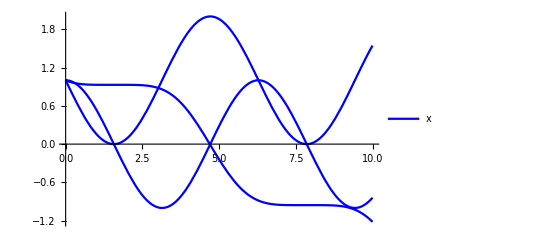

```mathematica
Plot[sol,{t,0,10}, PlotStyle->{Red, Black, Blue}, PlotLegends->LineLegend[{"x","y","z"}, LegendFunction->"Frame",LabelStyle->18]]
```